## Fig1：模型图及能级流程图

## Fig2：修正时间冗余函数与文献中的时间冗余函数

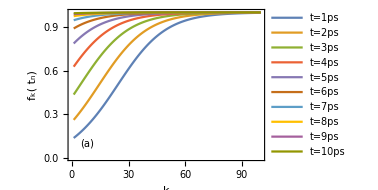

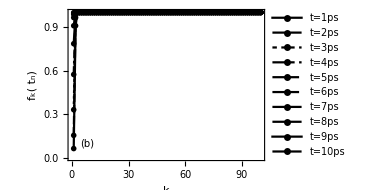

```mathematica
f[k_,t_]:=1/14 (Tanh[t/4+k/35]+13/(1+15 ⅇ^(-0.02 (40 t+4 k-1))));
tvalues=Range[1,10,1];kvalues=Range[0,99,1];
Table[f[k,t],{t,tvalues},{k,kvalues}];
ListLinePlot[Table[f[k,t],{t,tvalues},{k,kvalues}],Epilog->Text[Style["(a)",10],{8,0.1}],PlotRange->All,PlotStyle->Thickness[0.0001]/@ColorData["DarkRainbow","ColorList"],PlotLegends->Placed[LineLegend[Table["t="<>ToString[NumberForm[tvalues[[i]],{1,1}]]<>"ps",{i,1,Length[tvalues]}],LegendMarkerSize->8,LabelStyle->8],Scaled[{0.88,0.55}]],FrameLabel->{"k","f_k( t_n)"},FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],Frame->True,AspectRatio->0.68,ImageSize->280]

f[k_,t_]:=1/ (1+15 ⅇ^(-( t+5 k-1)));
tvalues=Range[1,10,1];kvalues=Range[0,99,1];
Table[f[k,t],{t,tvalues},{k,kvalues}];
mainplot=ListLinePlot[Table[f[k,t],{t,tvalues},{k,kvalues}],Epilog->Text[Style["(b)",10],{10,0.1}],PlotRange->All,PlotTheme->"Monochrome",PlotLegends->Placed[LineLegend[Table["t="<>ToString[NumberForm[tvalues[[i]],{1,1}]]<>"ps",{i,1,Length[tvalues]}],LegendMarkerSize->8,LabelStyle->8],Scaled[{0.88,0.55}]],FrameLabel->{"k","f_k( t_n)"},FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],Frame->True,AspectRatio->0.68,ImageSize->280];
insetPlot=ListLinePlot[Table[f[k,t],{t,tvalues},{k,0,4,1}],PlotRange->All,PlotTheme->"Monochrome",FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],Frame->True,AspectRatio->0.68,ImageSize->180];
Show[mainplot,Epilog->{Text[Style["(b)",10],{8,0.1}],Inset[insetPlot,{78,0.15},(*子图位于主图右下方15%位置*){Right,Bottom},Scaled[0.7]  (*子图大小为原图的70%*)]}]
```

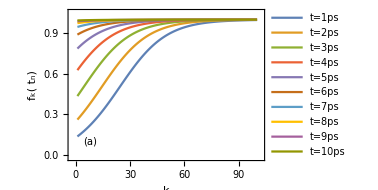
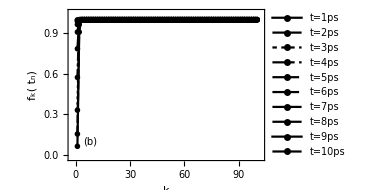

## Fig3： 7ps内的预测与理论值

#### 1-ρ_11理论与预测

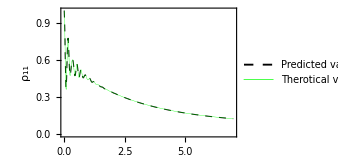

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["train_combined_1.csv"];
numericalData=Rest[data]; (*跳过表头*)
(*Print[numericalData];*)
(*提取列*)
xValues=numericalData[[All,1]];
fValues={f1Values,f2Values};
  f1Values=numericalData[[All,2]];
  f2Values=numericalData[[All,3]];

ListLinePlot[{Transpose[{xValues/100,f1Values}],Transpose[{xValues/100,f2Values}]},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green],Directive[Thickness[0.01],Red,Thick]     (*红色实线，较粗*)},
FrameLabel->{"t (ps)","ρ_11",FontSize->15},PlotLegends->Placed[LineLegend[{"Predicted values","Therotical values"},LegendMarkerSize->16,LabelStyle->10],Scaled[{0.58,0.55}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->250]
```

#### 2-ρ_22理论与预测

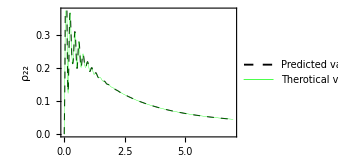

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["train_combined_2.csv"];
numericalData=Rest[data]; (*跳过表头*)
(*Print[numericalData];*)
(*提取列*)
xValues=numericalData[[All,1]];
fValues={f1Values,f2Values};
  f1Values=numericalData[[All,2]];
  f2Values=numericalData[[All,3]];

ListLinePlot[{Transpose[{xValues/100,f1Values}],Transpose[{xValues/100,f2Values}]},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green],Directive[Thickness[0.01],Red,Thick]     (*红色实线，较粗*)},
FrameLabel->{"t (ps)","ρ_22",FontSize->15},PlotLegends->Placed[LineLegend[{"Predicted values","Therotical values"},LegendMarkerSize->16,LabelStyle->10],Scaled[{0.58,0.55}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->250]
```

#### 3-ρ_33理论与预测

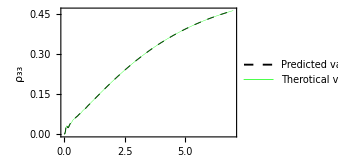

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["train_combined_3.csv"];
numericalData=Rest[data]; (*跳过表头*)
(*Print[numericalData];*)
(*提取列*)
xValues=numericalData[[All,1]];
fValues={f1Values,f2Values};
  f1Values=numericalData[[All,2]];
  f2Values=numericalData[[All,3]];

ListLinePlot[{Transpose[{xValues/100,f1Values}],Transpose[{xValues/100,f2Values}]},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green],Directive[Thickness[0.01],Red,Thick]     (*红色实线，较粗*)},
FrameLabel->{"t (ps)","ρ_33",FontSize->15},PlotLegends->Placed[LineLegend[{"Predicted values","Therotical values"},LegendMarkerSize->16,LabelStyle->10],Scaled[{0.58,0.55}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->250]
```

#### 4-ρ_44理论与预测

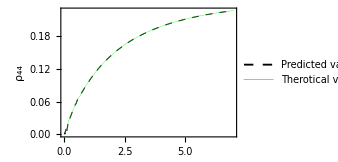

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["train_combined_4.csv"];

numericalData=Rest[data]; (*跳过表头*)
(*Print[numericalData];*)
(*提取列*)
xValues=numericalData[[All,1]];
fValues={f1Values,f2Values};
  f1Values=numericalData[[All,2]];
  f2Values=numericalData[[All,3]];

ListLinePlot[{Transpose[{xValues/100,f1Values}],Transpose[{xValues/100,f2Values}]},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green],Directive[Thickness[0.01],Red,Thick]     (*红色实线，较粗*)},
FrameLabel->{"t (ps)","ρ_44",FontSize->15},PlotLegends->Placed[LineLegend[{"Predicted values","Therotical values"},LegendMarkerSize->16,LabelStyle->10],Scaled[{0.58,0.55}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->250]
```

#### 5-ρ_55理论与预测

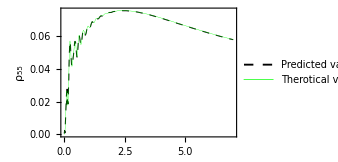

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["train_combined_5.csv"];

numericalData=Rest[data]; (*跳过表头*)
(*Print[numericalData];*)
(*提取列*)
xValues=numericalData[[All,1]];
fValues={f1Values,f2Values};
  f1Values=numericalData[[All,2]];
  f2Values=numericalData[[All,3]];

ListLinePlot[{Transpose[{xValues/100,f1Values}],Transpose[{xValues/100,f2Values}]},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green],Directive[Thickness[0.01],Red,Thick]     (*红色实线，较粗*)},
FrameLabel->{"t (ps)","ρ_55",FontSize->15},PlotLegends->Placed[LineLegend[{"Predicted values","Therotical values"},LegendMarkerSize->16,LabelStyle->10],Scaled[{0.58,0.55}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->250]
```

#### 6-ρ_66理论与预测

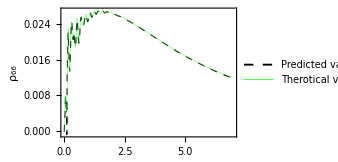

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["train_combined_6.csv"];

numericalData=Rest[data]; (*跳过表头*)
(*Print[numericalData];*)
(*提取列*)
xValues=numericalData[[All,1]];
fValues={f1Values,f2Values};
  f1Values=numericalData[[All,2]];
  f2Values=numericalData[[All,3]];

ListLinePlot[{Transpose[{xValues/100,f1Values}],Transpose[{xValues/100,f2Values}]},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green],Directive[Thickness[0.01],Red,Thick]     (*红色实线，较粗*)},
FrameLabel->{"t (ps)","ρ_66",FontSize->15},PlotLegends->Placed[LineLegend[{"Predicted values","Therotical values"},LegendMarkerSize->16,LabelStyle->10],Scaled[{0.58,0.55}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->250]
```

#### 7-ρ_77理论与预测

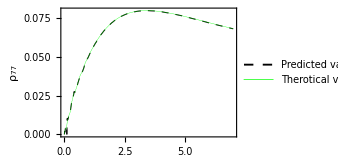

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["train_combined_7.csv"];

numericalData=Rest[data]; (*跳过表头*)
(*Print[numericalData];*)
(*提取列*)
xValues=numericalData[[All,1]];
fValues={f1Values,f2Values};
  f1Values=numericalData[[All,2]];
  f2Values=numericalData[[All,3]];

ListLinePlot[{Transpose[{xValues/100,f1Values}],Transpose[{xValues/100,f2Values}]},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green],Directive[Thickness[0.01],Red,Thick]     (*红色实线，较粗*)},
FrameLabel->{"t (ps)","ρ_77",FontSize->15},PlotLegends->Placed[LineLegend[{"Predicted values","Therotical values"},LegendMarkerSize->16,LabelStyle->10],Scaled[{0.58,0.55}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->250]
```

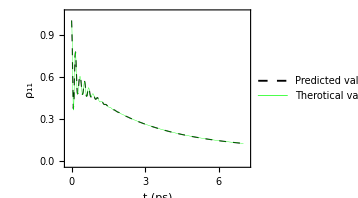
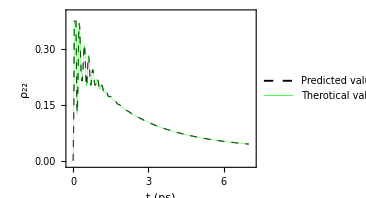
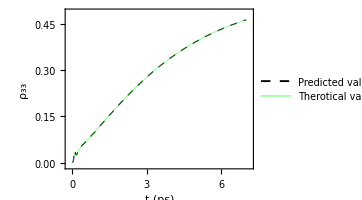
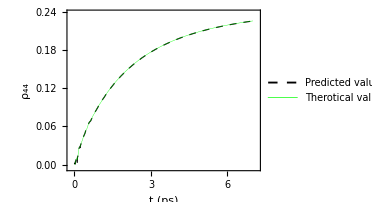
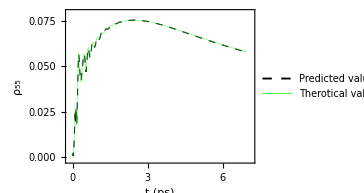
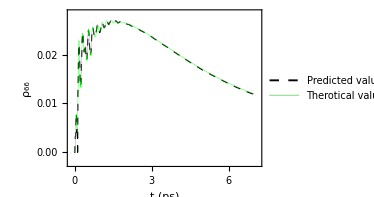
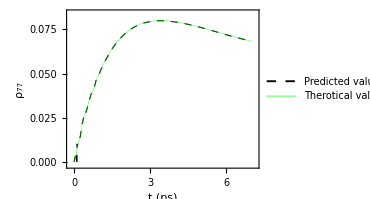

## Fig4: 100ps内的预测与理论值

#### 1-ρ_11理论与预测

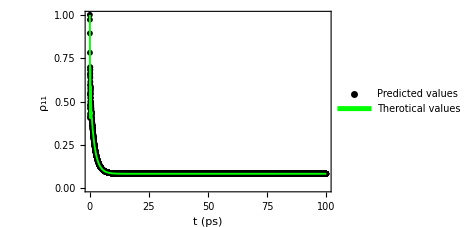

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["test_combined_1.csv"];
numericalData=Rest[data]; (*跳过表头*)
(*Print[numericalData];*)
(*提取列*)
xValues=numericalData[[All,1]];
f1Values=numericalData[[All,2]];
 f2Values=numericalData[[All,3]];

P1=ListPlot[{Transpose[{xValues/100,f2Values}]},(*ScalingFunctions->{"Log"},*)PlotRange->All,PlotMarkers->{"●",6},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green]},
FrameLabel->{"t (ps)","ρ_11",FontSize->15},PlotLegends->Placed[LineLegend[{"Predicted values","Therotical values"},LegendMarkerSize->6,LabelStyle->10],Scaled[{0.18,0.90}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->350];
P2=ListLinePlot[{Transpose[{xValues/100,f2Values}]},(*ScalingFunctions->{"Log"},*)PlotRange->All,PlotStyle->{(*Directive[Thickness[0.003],Black,Dashed],*)Directive[Thickness[0.004],Green]},
FrameLabel->{"t (ps)","ρ_11",FontSize->15},PlotLegends->Placed[LineLegend[{"Therotical values"},LegendMarkerSize->8,LabelStyle->10],Scaled[{0.18,0.80}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->350];
mainplot=Show[P1,P2];
P3=ListPlot[{Transpose[{xValues/100,f2Values}]},ScalingFunctions->{"Log"},PlotRange->All,PlotMarkers->{"●",6},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green],Directive[Thickness[0.01],Red,Thick]},
PlotLegends->Placed[LineLegend[{"Predicted values","Therotical values"},LegendMarkerSize->6,LabelStyle->6],Scaled[{0.80,0.85}]],LabelStyle->Directive[FontFamily->"Times",FontSize->8],AspectRatio->0.85,Frame->True,ImageSize->350];
P4=ListLinePlot[{Transpose[{xValues/100,f2Values}]},ScalingFunctions->{"Log"},PlotRange->All,PlotStyle->{(*Directive[Thickness[0.003],Black,Dashed],*)Directive[Thickness[0.004],Green],Directive[Thickness[0.01],Red,Thick]},
PlotLegends->Placed[LineLegend[{"Therotical values"},LegendMarkerSize->8,LabelStyle->6],Scaled[{0.80,0.75}]],LabelStyle->Directive[FontFamily->"Times",FontSize->8],AspectRatio->0.85,Frame->True,ImageSize->350];
insertplot=Show[P3,P4];
Show[mainplot,Epilog->Inset[insertplot,{99,0.14},(*子图位于主图右下方15%位置*){Right,Bottom},Scaled[0.75]  (*子图大小为原图的70%*)]]
```

#### 2-ρ_22理论与预测

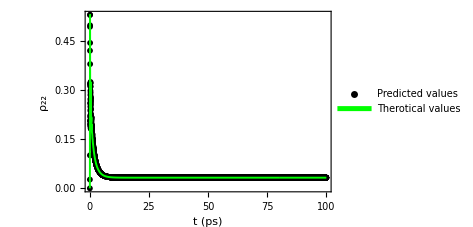

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["test_combined_2.csv"];

numericalData=Rest[data]; (*跳过表头*)
(*Print[numericalData];*)
(*提取列*)
xValues=numericalData[[All,1]];
fValues={f1Values,f2Values};
  f1Values=numericalData[[All,2]];
  f2Values=numericalData[[All,3]];
P1=ListPlot[{Transpose[{xValues/100,f2Values}]},(*ScalingFunctions->{"Log"},*)PlotRange->All,PlotMarkers->{"●",6},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green],Directive[Thickness[0.01],Red,Thick]},
FrameLabel->{"t (ps)","ρ_22",FontSize->15},PlotLegends->Placed[LineLegend[{"Predicted values","Therotical values"},LegendMarkerSize->6,LabelStyle->10],Scaled[{0.18,0.92}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->350];
P2=ListLinePlot[{Transpose[{xValues/100,f2Values}]},(*ScalingFunctions->{"Log"},*)PlotRange->All,PlotStyle->{(*Directive[Thickness[0.003],Black,Dashed],*)Directive[Thickness[0.004],Green],Directive[Thickness[0.01],Red,Thick]},
FrameLabel->{"t (ps)","ρ_22",FontSize->15},PlotLegends->Placed[LineLegend[{"Therotical values"},LegendMarkerSize->8,LabelStyle->10],Scaled[{0.18,0.82}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->350];
mainplot=Show[P1,P2];
P3=ListPlot[{Transpose[{xValues/100,f2Values}]},ScalingFunctions->{"Log"},PlotRange->All,PlotMarkers->{"●",6},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green],Directive[Thickness[0.01],Red,Thick]},
PlotLegends->Placed[LineLegend[{"Predicted values","Therotical values"},LegendMarkerSize->6,LabelStyle->6],Scaled[{0.78,0.85}]],LabelStyle->Directive[FontFamily->"Times",FontSize->8],AspectRatio->0.65,Frame->True,ImageSize->350];
P4=ListLinePlot[{Transpose[{xValues/100,f2Values}]},ScalingFunctions->{"Log"},PlotRange->All,PlotStyle->{(*Directive[Thickness[0.003],Black,Dashed],*)Directive[Thickness[0.004],Green],Directive[Thickness[0.01],Red,Thick]},
PlotLegends->Placed[LineLegend[{"Therotical values"},LegendMarkerSize->6,LabelStyle->6],Scaled[{0.78,0.75}]],LabelStyle->Directive[FontFamily->"Times",FontSize->8],AspectRatio->0.65,Frame->True,ImageSize->350];
insertplot=Show[P3,P4];
Show[mainplot,Epilog->Inset[insertplot,{99,0.05},(*子图位于主图右下方15%位置*){Right,Bottom},Scaled[0.70]  (*子图大小为原图的70%*)]]
```

#### 3-ρ_33理论与预测

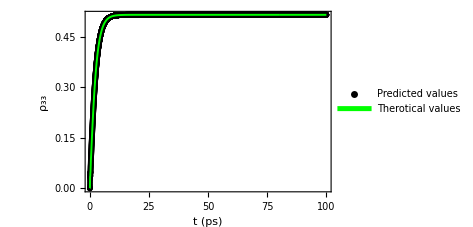

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["test_combined_3.csv"];

numericalData=Rest[data]; (*跳过表头*)
(*Print[numericalData];*)
(*提取列*)
xValues=numericalData[[All,1]];
fValues={f1Values,f2Values};
  f1Values=numericalData[[All,2]];
  f2Values=numericalData[[All,3]];
P1=ListPlot[{Transpose[{xValues/100,f2Values}]},(*ScalingFunctions->{"Log"},*)PlotRange->All,PlotMarkers->{"●",6},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green],Directive[Thickness[0.01],Red,Thick]},
FrameLabel->{"t (ps)","ρ_33",FontSize->15},PlotLegends->Placed[LineLegend[{"Predicted values","Therotical values"},LegendMarkerSize->6,LabelStyle->10],Scaled[{0.82,0.88}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->350];
P2=ListLinePlot[{Transpose[{xValues/100,f2Values}]},(*ScalingFunctions->{"Log"},*)PlotRange->All,PlotStyle->{(*Directive[Thickness[0.003],Black,Dashed],*)Directive[Thickness[0.004],Green],Directive[Thickness[0.01],Red,Thick]},
FrameLabel->{"t (ps)","ρ_33",FontSize->15},PlotLegends->Placed[LineLegend[{"Therotical values"},LegendMarkerSize->8,LabelStyle->10],Scaled[{0.82,0.78}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->350];
mainplot=Show[P1,P2];
P3=ListPlot[{Transpose[{xValues/100,f2Values}]},ScalingFunctions->{"Log"},PlotRange->All,PlotMarkers->{"●",6},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green],Directive[Thickness[0.01],Red,Thick]},
PlotLegends->Placed[LineLegend[{"Predicted values","Therotical values"},LegendMarkerSize->6,LabelStyle->6],Scaled[{0.8,0.25}]],LabelStyle->Directive[FontFamily->"Times",FontSize->8],AspectRatio->0.65,Frame->True,ImageSize->350];
P4=ListLinePlot[{Transpose[{xValues/100,f2Values}]},ScalingFunctions->{"Log"},PlotRange->All,PlotStyle->{(*Directive[Thickness[0.003],Black,Dashed],*)Directive[Thickness[0.004],Green],Directive[Thickness[0.01],Red,Thick]},
PlotLegends->Placed[LineLegend[{"Therotical values"},LegendMarkerSize->8,LabelStyle->6],Scaled[{0.8,0.15}]],LabelStyle->Directive[FontFamily->"Times",FontSize->8],AspectRatio->0.65,Frame->True,ImageSize->350];
insertplot=Show[P3,P4];
Show[mainplot,Epilog->Inset[insertplot,{99,0.002},(*子图位于主图右下方15%位置*){Right,Bottom},Scaled[0.70]  (*子图大小为原图的70%*)]]
```

#### 4-ρ_44理论与预测

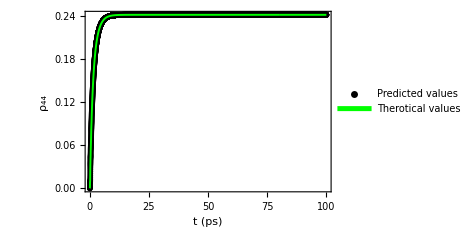

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["test_combined_4.csv"];
numericalData=Rest[data]; (*跳过表头*)
(*Print[numericalData];*)
(*提取列*)
xValues=numericalData[[All,1]];
fValues={f1Values,f2Values};
  f1Values=numericalData[[All,2]];
  f2Values=numericalData[[All,3]];
P1=ListPlot[{Transpose[{xValues/100,f2Values}]},(*ScalingFunctions->{"Log"},*)PlotRange->All,PlotMarkers->{"●",6},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green],Directive[Thickness[0.01],Red,Thick]},
FrameLabel->{"t (ps)","ρ_44",FontSize->15},PlotLegends->Placed[LineLegend[{"Predicted values","Therotical values"},LegendMarkerSize->6,LabelStyle->10],Scaled[{0.8,0.87}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->350];
P2=ListLinePlot[{Transpose[{xValues/100,f2Values}]},(*ScalingFunctions->{"Log"},*)PlotRange->All,PlotStyle->{(*Directive[Thickness[0.003],Black,Dashed],*)Directive[Thickness[0.004],Green],Directive[Thickness[0.01],Red,Thick]},
FrameLabel->{"t (ps)","ρ_44",FontSize->15},PlotLegends->Placed[LineLegend[{"Therotical values"},LegendMarkerSize->8,LabelStyle->10],Scaled[{0.8,0.77}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->350];
mainplot=Show[P1,P2];
P3=ListPlot[{Transpose[{xValues/100,f2Values}]},ScalingFunctions->{"Log"},PlotRange->All,PlotMarkers->{"●",6},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green],Directive[Thickness[0.01],Red,Thick]},
PlotLegends->Placed[LineLegend[{"Predicted values","Therotical values"},LegendMarkerSize->6,LabelStyle->6],Scaled[{0.78,0.25}]],LabelStyle->Directive[FontFamily->"Times",FontSize->8],AspectRatio->0.65,Frame->True,ImageSize->350];
P4=ListLinePlot[{Transpose[{xValues/100,f2Values}]},ScalingFunctions->{"Log"},PlotRange->All,PlotStyle->{(*Directive[Thickness[0.003],Black,Dashed],*)Directive[Thickness[0.004],Green],Directive[Thickness[0.01],Red,Thick]},
PlotLegends->Placed[LineLegend[{"Therotical values"},LegendMarkerSize->8,LabelStyle->6],Scaled[{0.78,0.15}]],LabelStyle->Directive[FontFamily->"Times",FontSize->8],AspectRatio->0.65,Frame->True,ImageSize->350];
insertplot=Show[P3,P4];
Show[mainplot,Epilog->Inset[insertplot,{99,0.001},(*子图位于主图右下方15%位置*){Right,Bottom},Scaled[0.70]  (*子图大小为原图的70%*)]]
```

#### 5-ρ_55理论与预测

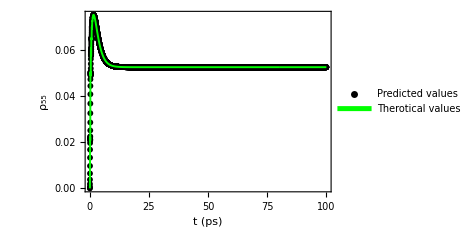

```mathematica
SetDirectory[NotebookDirectory[]];
 data=Import["test_combined_5.csv"];

numericalData=Rest[data]; (*跳过表头*)
(*Print[numericalData];*)
(*提取列*)
xValues=numericalData[[All,1]];
fValues={f1Values,f2Values};
  f1Values=numericalData[[All,2]];
  f2Values=numericalData[[All,3]];
P1=ListPlot[{Transpose[{xValues/100,f2Values}]},(*ScalingFunctions->{"Log"},*)PlotRange->All,PlotMarkers->{"●",6},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green],Directive[Thickness[0.01],Red,Thick]},
FrameLabel->{"t (ps)","ρ_55",FontSize->15},PlotLegends->Placed[LineLegend[{"Predicted values"},LegendMarkerSize->6,LabelStyle->10],Scaled[{0.20,0.23}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->350];
P2=ListLinePlot[{Transpose[{xValues/100,f2Values}]},(*ScalingFunctions->{"Log"},*)PlotRange->All,PlotStyle->{(*Directive[Thickness[0.003],Black,Dashed],*)Directive[Thickness[0.004],Green],Directive[Thickness[0.01],Red,Thick]},
FrameLabel->{"t (ps)","ρ_55",FontSize->15},PlotLegends->Placed[LineLegend[{"Therotical values"},LegendMarkerSize->8,LabelStyle->10],Scaled[{0.20,0.13}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->350];
mainplot=Show[P1,P2];
P3=ListPlot[{Transpose[{xValues/100,f2Values}]},ScalingFunctions->{"Log"},PlotRange->All,PlotMarkers->{"●",6},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green],Directive[Thickness[0.01],Red,Thick]},
PlotLegends->Placed[LineLegend[{"Predicted values"},LegendMarkerSize->6,LabelStyle->6],Scaled[{0.80,0.22}]],LabelStyle->Directive[FontFamily->"Times",FontSize->8],AspectRatio->0.65,Frame->True,ImageSize->350];
P4=ListLinePlot[{Transpose[{xValues/100,f2Values}]},ScalingFunctions->{"Log"},PlotRange->All,PlotStyle->{(*Directive[Thickness[0.003],Black,Dashed],*)Directive[Thickness[0.004],Green],Directive[Thickness[0.01],Red,Thick]},
PlotLegends->Placed[LineLegend[{"Therotical values"},LegendMarkerSize->8,LabelStyle->6],Scaled[{0.80,0.10}]],LabelStyle->Directive[FontFamily->"Times",FontSize->8],AspectRatio->0.65,Frame->True,ImageSize->350];
insertplot=Show[P3,P4];
Show[mainplot,Epilog->Inset[insertplot,{99,0.001},(*子图位于主图右下方15%位置*){Right,Bottom},Scaled[0.62]  (*子图大小为原图的70%*)]]
```

#### 6-ρ_66理论与预测

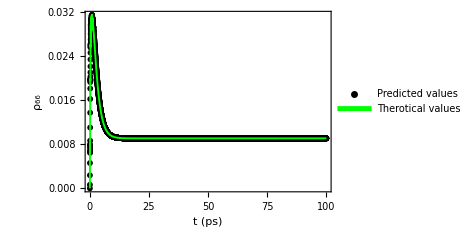

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["test_combined_6.csv"];
numericalData=Rest[data]; (*跳过表头*)
(*Print[numericalData];*)
(*提取列*)
xValues=numericalData[[All,1]];
fValues={f1Values,f2Values};
  f1Values=numericalData[[All,2]];
  f2Values=numericalData[[All,3]];

P1=ListPlot[{Transpose[{xValues/100,f2Values}]},(*ScalingFunctions->{"Log"},*)PlotRange->All,PlotMarkers->{"●",6},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green]},
FrameLabel->{"t (ps)","ρ_66",FontSize->15},PlotLegends->Placed[LineLegend[{"Predicted values","Therotical values"},LegendMarkerSize->6,LabelStyle->10],Scaled[{0.80,0.18}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->350];
P2=ListLinePlot[{Transpose[{xValues/100,f2Values}]},(*ScalingFunctions->{"Log"},*)PlotRange->All,PlotStyle->{(*Directive[Thickness[0.003],Black,Dashed],*)Directive[Thickness[0.004],Green]},
FrameLabel->{"t (ps)","ρ_66",FontSize->15},PlotLegends->Placed[LineLegend[{"Therotical values"},LegendMarkerSize->8,LabelStyle->10],Scaled[{0.80,0.08}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->350];
mainplot=Show[P1,P2];
P3=ListPlot[{Transpose[{xValues/100,f2Values}]},ScalingFunctions->{"Log"},PlotRange->All,PlotMarkers->{"●",6},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green],Directive[Thickness[0.01],Red,Thick]},
PlotLegends->Placed[LineLegend[{"Predicted values"},LegendMarkerSize->6,LabelStyle->6],Scaled[{0.52,0.25}]],LabelStyle->Directive[FontFamily->"Times",FontSize->8],AspectRatio->0.60,Frame->True,ImageSize->350];
P4=ListLinePlot[{Transpose[{xValues/100,f2Values}]},ScalingFunctions->{"Log"},PlotRange->All,PlotStyle->{(*Directive[Thickness[0.003],Black,Dashed],*)Directive[Thickness[0.004],Green],Directive[Thickness[0.01],Red,Thick]},
PlotLegends->Placed[LineLegend[{"Therotical values"},LegendMarkerSize->6,LabelStyle->6],Scaled[{0.52,0.15}]],LabelStyle->Directive[FontFamily->"Times",FontSize->8],AspectRatio->0.60,Frame->True,ImageSize->350];
insertplot=Show[P3,P4];Show[mainplot,Epilog->Inset[insertplot,{99,0.010},(*子图位于主图右下方15%位置*){Right,Bottom},Scaled[0.70]  (*子图大小为原图的70%*)]]
```

### 7-ρ_77理论与预测

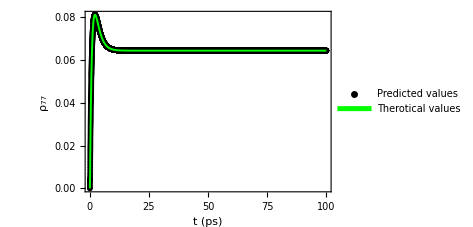

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["test_combined_7.csv"];
numericalData=Rest[data]; (*跳过表头*)
(*Print[numericalData];*)
(*提取列*)
xValues=numericalData[[All,1]];
fValues={f1Values,f2Values};
  f1Values=numericalData[[All,2]];
  f2Values=numericalData[[All,3]];

P1=ListPlot[{Transpose[{xValues/100,f2Values}]},(*ScalingFunctions->{"Log"},*)PlotRange->All,PlotMarkers->{"●",6},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green],Directive[Thickness[0.01],Red,Thick]},
FrameLabel->{"t (ps)","ρ_77",FontSize->15},PlotLegends->Placed[LineLegend[{"Predicted values","Therotical values"},LegendMarkerSize->6,LabelStyle->8],Scaled[{0.18,0.20}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->350];
P2=ListLinePlot[{Transpose[{xValues/100,f2Values}]},(*ScalingFunctions->{"Log"},*)PlotRange->All,PlotStyle->{(*Directive[Thickness[0.003],Black,Dashed],*)Directive[Thickness[0.004],Green],Directive[Thickness[0.01],Red,Thick]},
FrameLabel->{"t (ps)","ρ_77",FontSize->15},PlotLegends->Placed[LineLegend[{"Therotical values"},LegendMarkerSize->8,LabelStyle->8],Scaled[{0.18,0.1}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],AspectRatio->0.65,Frame->True,ImageSize->350];
mainplot=Show[P1,P2];
P3=ListPlot[{Transpose[{xValues/100,f2Values}]},ScalingFunctions->{"Log"},PlotRange->All,PlotMarkers->{"●",6},PlotStyle->{Directive[Thickness[0.003],Black,Dashed],Directive[Thickness[0.001],Green],Directive[Thickness[0.01],Red,Thick]},
PlotLegends->Placed[LineLegend[{"Predicted values","Therotical values"},LegendMarkerSize->4,LabelStyle->6],Scaled[{0.80,0.22}]],LabelStyle->Directive[FontFamily->"Times",FontSize->8],AspectRatio->0.65,Frame->True,ImageSize->350];
P4=ListLinePlot[{Transpose[{xValues/100,f2Values}]},ScalingFunctions->{"Log"},PlotRange->All,PlotStyle->{(*Directive[Thickness[0.003],Black,Dashed],*)Directive[Thickness[0.004],Green],Directive[Thickness[0.01],Red,Thick]},
PlotLegends->Placed[LineLegend[{"Therotical values"},LegendMarkerSize->8,LabelStyle->6],Scaled[{0.80,0.10}]],LabelStyle->Directive[FontFamily->"Times",FontSize->8],AspectRatio->0.65,Frame->True,ImageSize->350];
insetPlot=Show[P3,P4];
Show[mainplot,Epilog->Inset[insetPlot,{99,0.002},(*子图位于主图右下方15%位置*){Right,Bottom},Scaled[0.65]  (*子图大小为原图的50%*)]]
```

### 8-ARE

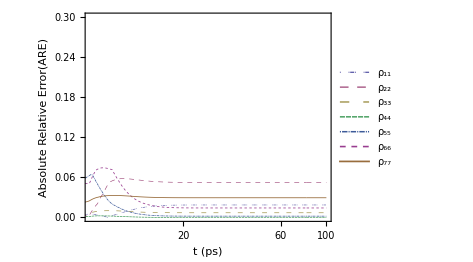

```mathematica
(*第1步：导入与处理数据*)
SetDirectory[NotebookDirectory[]]; (*设置当前目录为笔记本所在目录*)
filePaths=Table["test_combined_"<>ToString[i]<>".csv",{i,1,7}];
 
data=Import[#]&/@filePaths;(*使用 Import 函数批量导入 CSV 文件，并存储为 data 列表*)
numericalData=Rest/@data;(*使用 Rest 函数去掉每个数据表的表头，仅保留数值部分*)
xValues=numericalData[[1,All,1]];(*提取横坐标 xValues（假设所有文件的第1列相同，因此取第一个文件即可）*)
fValues1=Table[numericalData[[i,All,2]]-numericalData[[i,All,3]],{i,1,7}];(*计算每组数据的差值（第2列减第3列），生成 fValues 列表*)
fValues2=Table[Abs[(numericalData[[i,All,2]]-numericalData[[i,All,3]])/numericalData[[i,All,2]]],{i,1,7}];
(*第2步：设置图例*)
legends=Table["Curve "<>ToString[i],{i,1,7}];(*为每条曲线生成对应的图例标签，Curve 1 到 Curve 7*)

(*第3步：绘制图像*)
mainplot=ListLinePlot[Transpose[{xValues/100,#}]&/@fValues2,(*将 xValues/100 与每组 fValues 合并为坐标对*)ScalingFunctions->{"Log"},(*使用对数缩放函数，使纵坐标对数化*)PlotRange->{{7,100},{0,0.3}},(*自动调整绘图范围*)PlotStyle->Table[Directive[Thickness[0.001+i/10000],ColorData[1][i],(*为每条曲线设置不同线型*)Switch[i,1,Dashing[{0.001,0.01,0.001,0.001,0.005,0.001}],(*实线*)2,Dashing[{0.01,0.01}],(*虚线*)3,Dashing[{0.01,0.015}],(*长虚线*)4,Dashing[{0.005,0.001}],(*短虚线*)5,Dashing[{0.001,0.001,0.005,0.001}],(*点划线*)6,Dashing[{0.005,0.005}],(*点线*)7, Dashing[{}](*双点划线*)]],{i,1,7}],FrameLabel->{"t (ps)","Absolute Relative Error(ARE)",FontSize->15},(*设置坐标轴标签，x 轴为时间，y 轴为密度矩阵元素*)PlotLegends->Placed[LineLegend[Table[Subscript["ρ",ToString[i]<>ToString[i]],{i,1,7}],LegendMarkerSize->10,LabelStyle->7,LegendLayout->{"Column",4}],Scaled[{0.75,0.88}]],LabelStyle->Directive[FontFamily->"Times",FontSize->12],(*设置全局标签字体样式，使用 Times 字体和适中字号*)AspectRatio->0.75,(*设置纵横比*)Frame->True,(*开启图框显示*)ImageSize->350 (*设置图像尺寸为400像素宽*),FrameTicks->{{Automatic,Automatic},(*Y轴保持自动刻度*){Union[{{7,"7",{0.02,0},Thickness[0.003]}},(*确保显示数字7*)Charting`FindTicks[{0,100},{0,100}][7,100] (*保留其他自动刻度*)],Automatic}}];

insetPlot=ListLinePlot[Transpose[{xValues/100,#}]&/@fValues1,ScalingFunctions->{"Log"},PlotRange->{{7,100},{-0.0038,0.0055}},PlotStyle->Table[Directive[Thickness[0.001+i/8000],ColorData[1][i],(*为每条曲线设置不同线型*)Switch[i,1,Dashing[{0.001,0.01,0.001,0.001,0.005,0.001}],(*实线*)2,Dashing[{0.01,0.01}],(*虚线*)3,Dashing[{0.01,0.015}],(*长虚线*)4,Dashing[{0.005,0.001}],(*短虚线*)5,Dashing[{0.001,0.001,0.005,0.001}],(*点划线*)6,Dashing[{0.005,0.005}],(*点线*)7, Dashing[{}](*双点划线*)]],{i,1,7}],FrameLabel->{" ","Loss for populations"},(*PlotLegends->Placed[LineLegend[Table[Subscript["ρ",ToString[i]<>ToString[i]],{i,1,7}],LegendMarkerSize->12,LabelStyle->8,LegendLayout->{"Column",4}],Scaled[{0.7,0.14}]],*)LabelStyle->Directive[FontFamily->"Times",FontSize->8],AspectRatio->0.55,Frame->True,ImageSize->300,FrameTicks->{{Automatic,Automatic},(*Y轴保持自动刻度*){Union[{{7,"7",{0.02,0},Thickness[0.003]}},(*确保显示数字7*)Charting`FindTicks[{0,100},{0,100}][7,100] (*保留其他自动刻度*)],Automatic}}];

pp=Show[mainplot,Epilog->{Inset[insetPlot,{4.55,0.042},(*子图位于主图右下方15%位置*){Right,Bottom},Scaled[0.9]  (*子图大小为原图的80%*)]}]
```